# Solving the Schrödinger equation for finite potential well in several configurations

Leonel A. Cabrera, ...
School of Physical Sciences and Nanotechnology, Yachay Tech University, Urcuqui, Ecuador

## Single finite potential well

Let’s define the potential, we need the piecewise function: esc+pw+esc

```mathematica
v[x_]:=Piecewise[{{v0, x<-a/2}, {0, -a/2<=x<=a/2}, {v0, x>a/2}}]
```

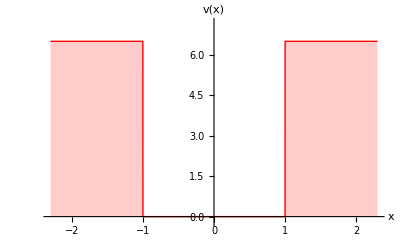

```mathematica
v[x]//Plot[#/.{v0->6.5(*Hartrees*),a->2(*Bohr radius*)},{x,-2.3,2.3},
AxesLabel->{"x","v(x)"},
BaseStyle->{"FontFamily"->"Helvetica",FontSize->18},
PlotStyle->{Red,Thick},
PlotRange->{Automatic,{-0.2,7.2}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis
]&
```

```mathematica
eq1=-1/2 ϕ''[x]+v0 ϕ[x]==ℰ ϕ[x](*The equation is in atomic units*)
```

v0 ϕ[x]-ϕ''[x]/2==ℰ ϕ[x]

```mathematica
eq2=-1/2 ϕ''[x]+0 ϕ[x]==ℰ ϕ[x]
```

-1/2 ϕ''[x]==ℰ ϕ[x]

```mathematica
eq3=-1/2 ϕ''[x]+v0 ϕ[x]==ℰ ϕ[x]
```

v0 ϕ[x]-ϕ''[x]/2==ℰ ϕ[x]

```mathematica
DSolve[eq1,ϕ[x],x]
```

{{ϕ[x]→ⅇ^(√2 x √(v0-ℰ)) C[1]+ⅇ^(-√2 x √(v0-ℰ)) C[2]}}

```mathematica
{ϕ[x]->ⅇ^(√2 x √(v0-ℰ)) C[1]}
```

{ϕ[x]→ⅇ^(√2 x √(v0-ℰ)) C[1]}

```mathematica
DSolve[eq2,ϕ[x],x]
```

{{ϕ[x]→C[1] Cos[√2 x √ℰ]+C[2] Sin[√2 x √ℰ]}}

```mathematica
DSolve[eq3,ϕ[x],x]
```

{{ϕ[x]→ⅇ^(√2 x √(v0-ℰ)) C[1]+ⅇ^(-√2 x √(v0-ℰ)) C[2]}}

```mathematica
{ϕ[x]->ⅇ^(-√2 x √(v0-ℰ)) C[2]}
```

{ϕ[x]→ⅇ^(-√2 x √(v0-ℰ)) C[2]}

Let’s define α = √(2 ( v0 -ℰ)) and β=√(2ℰ)

```mathematica
Do[Subscript[c,i]=.,{i,4}];
Do[Subscript[ϕ,i]=.,{i,3}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x]+Subscript[c, 3] Sin[β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x];
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ϕ_1 not found.

Unset::norep: Assignment on Subscript for ϕ_2 not found.

Unset::norep: Assignment on Subscript for ϕ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/.x->-a/2)==0
```

ⅇ^(-(a α)/2) c_1-Cos[(a β)/2] c_2+Sin[(a β)/2] c_3==0

```mathematica
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/.x->-a/2)==0
```

ⅇ^(-(a α)/2) α c_1-β Sin[(a β)/2] c_2-β Cos[(a β)/2] c_3==0

```mathematica
ⅇ^(-(a α)/2) α Subscript[c, 1]-β Sin[(a β)/2] Subscript[c, 2]-β Cos[(a β)/2] Subscript[c, 3]==0
```

ⅇ^(-(a α)/2) α c_1-β Sin[(a β)/2] c_2-β Cos[(a β)/2] c_3==0

```mathematica
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/.x->a/2)==0
```

Cos[(a β)/2] c_2+Sin[(a β)/2] c_3-ⅇ^(-(a α)/2) c_4==0

```mathematica
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/.x->a/2)==0
```

-β Sin[(a β)/2] c_2+β Cos[(a β)/2] c_3+ⅇ^(-(a α)/2) α c_4==0

```mathematica
mat=CoefficientArrays[Table[eq[i],{i,4}],Table[Subscript[c, i],{i,4}]][[2]]//Normal
%//MatrixForm
```

{{ⅇ^(-(a α)/2),-Cos[(a β)/2],Sin[(a β)/2],0},{ⅇ^(-(a α)/2) α,-β Sin[(a β)/2],-β Cos[(a β)/2],0},{0,Cos[(a β)/2],Sin[(a β)/2],-ⅇ^(-(a α)/2)},{0,-β Sin[(a β)/2],β Cos[(a β)/2],ⅇ^(-(a α)/2) α}}

(ⅇ^(-(a α)/2) | -Cos[(a β)/2] | Sin[(a β)/2] | 0
ⅇ^(-(a α)/2) α | -β Sin[(a β)/2] | -β Cos[(a β)/2] | 0
0 | Cos[(a β)/2] | Sin[(a β)/2] | -ⅇ^(-(a α)/2)
0 | -β Sin[(a β)/2] | β Cos[(a β)/2] | ⅇ^(-(a α)/2) α)

```mathematica
Det[mat]
```

2 ⅇ^(-a α) α β Cos[(a β)/2]^2+2 ⅇ^(-a α) α^2 Cos[(a β)/2] Sin[(a β)/2]-2 ⅇ^(-a α) β^2 Cos[(a β)/2] Sin[(a β)/2]-2 ⅇ^(-a α) α β Sin[(a β)/2]^2

We have to solve this numerically:

```mathematica
mat2=(mat/.{α->√(2 (v0 -ℰ)),β->√(2ℰ)})/.{v0->6.5,a->2}//FullSimplify
```

{{ⅇ^(-1.41421 √(6.5-ℰ)),-Cos[√2 √ℰ],Sin[√2 √ℰ],0},{1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[√2 √ℰ],-√2 √ℰ Cos[√2 √ℰ],0},{0,Cos[√2 √ℰ],Sin[√2 √ℰ],-ⅇ^(-1.41421 √(6.5-ℰ))},{0,-√2 √ℰ Sin[√2 √ℰ],√2 √ℰ Cos[√2 √ℰ],1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ)}}

```mathematica
Solve[Det[mat2]==0,ℰ](*To see that is not possible to solve analitically*)
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[4. ⅇ^(-2.82843 √(6.5-ℰ)) √(6.5-ℰ) √ℰ Cos[√2 √ℰ]^2+26. ⅇ^(-2.82843 √(6.5-ℰ)) Cos[√2 √ℰ] Sin[√2 √ℰ]-8. ⅇ^(-2.82843 √(6.5-ℰ)) ℰ Cos[√2 √ℰ] Sin[√2 √ℰ]-4. ⅇ^(-2.82843 √(6.5-ℰ)) √(6.5-ℰ) √ℰ Sin[√2 √ℰ]^2==0,ℰ]

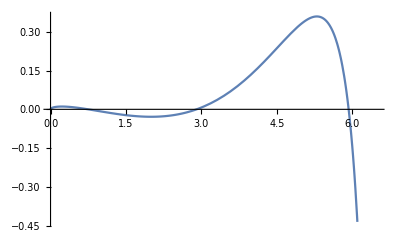

```mathematica
Plot[Det[mat2],{ℰ,0,6.5}]
```

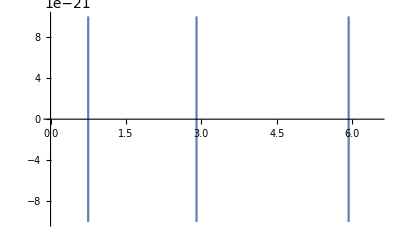

```mathematica
fig=Plot[Det[mat2],{ℰ,0,6.5},PlotRange->{-10^-20,10^-20}]
```

```mathematica
Reduce[Det[mat2]==0&&0<ℰ<6.5,ℰ]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ℰ==0.7495||ℰ==2.9032||ℰ==5.92714

```mathematica
(*fig[[1]]*)
```

```mathematica
(*fig[[1,1,1,3,1]][[2;;-1]]*)
```

```mathematica
aproxroots=fig[[1,1,1,3,1]][[2;;-1]]//Map[#[[1,1,1]]&,#]&//Sort
```

{0.748476,2.9027,5.92702}

```mathematica
rval=aproxroots//Map[FindRoot[Det[mat2],{ℰ,#}]&,#]&//Map[ℰ/.#&,#]&
```

{0.7495,2.9032,5.92714}

### Level 1

```mathematica
nval=1;
Do[Subscript[c,i]=.,{i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=(mat2/.{ℰ->rval[[nval]]}//NullSpace)[[1]]//Chop
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{0.705376,0.0699299,0,0.705376}

```mathematica
int=NIntegrate[Abs[Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]
```

0.00633217

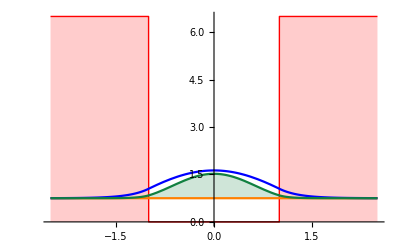

```mathematica
Plot[
{v[x],
ℰ,
ℰ+(1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]),
ℰ+(1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}])^2}/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,
{x,-2.5,2.5},
PlotRange->All,
PlotStyle->{{Red,Thick}(*Potential*),Orange(*Energy level*),Blue,RGBColor[0.0654154, 0.501808, 0.250996]},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}]
```

Let's integrate the “blue” line:

```mathematica
NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]
```

1.

```mathematica
NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-1/2,1/2}]
```

0.682785

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2 x/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.0000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 7.67615×10^-17 and 1.60642×10^-14 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2 x^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]//Chop
```

0.228641

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

0.478165

```mathematica
⟨p⟩=NIntegrate[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}](-ⅈ D[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}],x])/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.667984}. NIntegrate obtained 0.+2.28983×10^-16 ⅈ and 9.96422×10^-17 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}](- D[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}],{x,2}])/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]
```

1.15764

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

1.07594

```mathematica
Δx Δp
```

0.514476

### Level 2

```mathematica
nval=2;
Do[Subscript[c,i]=.,{i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=(mat2/.{ℰ->rval[[nval]]}//NullSpace)[[1]]//Chop
```

{-0.705261,0,0.0722025,0.705261}

```mathematica
int=NIntegrate[Abs[Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]
```

0.00715691

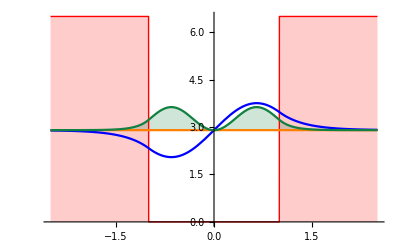

```mathematica
Plot[
{v[x],
ℰ,
ℰ+(1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]),
ℰ+(1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}])^2}/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,
{x,-2.5,2.5},
PlotRange->All,
PlotStyle->{{Red,Thick}(*Potential*),Orange(*Energy level*),Blue,RGBColor[0.0654154, 0.501808, 0.250996]},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}]
```

Let's integrate the “blue” line:

```mathematica
NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]
```

1.

```mathematica
NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-1/2,1/2}]
```

0.263194

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2 x/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.9999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 2.15106×10^-16 and 1.46294×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2 x^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]//Chop
```

0.548414

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

0.74055

```mathematica
⟨p⟩=NIntegrate[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}](-ⅈ D[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}],x])/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.0000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 0.+4.38885×10^-16 ⅈ and 1.58363×10^-13 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}](- D[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}],{x,2}])/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]
```

4.22948

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.05657

```mathematica
Δx Δp
```

1.52299

### Level 3

```mathematica
nval=3;
Do[Subscript[c,i]=.,{i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=(mat2/.{ℰ->rval[[nval]]}//NullSpace)[[1]]//Chop
```

{0.685361,-0.24609,0,0.685361}

```mathematica
int=NIntegrate[Abs[Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]
```

0.117138

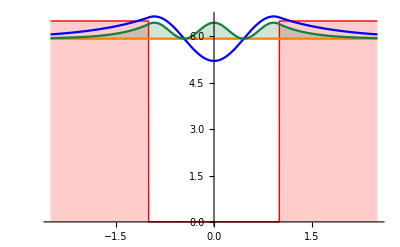

```mathematica
Plot[
{v[x],
ℰ,
ℰ+(1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]),
ℰ+(1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}])^2}/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,
{x,-2.5,2.5},
PlotRange->All,
PlotStyle->{{Red,Thick}(*Potential*),Orange(*Energy level*),Blue,RGBColor[0.0654154, 0.501808, 0.250996]},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}]
```

Let's integrate the “blue” line:

```mathematica
NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]
```

1.

```mathematica
NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-1/2,1/2}]
```

0.23621

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2 x/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.77168}. NIntegrate obtained -1.10502×10^-15 and 7.27872×10^-17 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]]^2 x^2/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]//Chop
```

1.27519

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)
```

1.12924

```mathematica
⟨p⟩=NIntegrate[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}](-ⅈ D[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}],x])/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.99999998206481784018499997731624644344006203056096637737937271595}. NIntegrate obtained 0.-8.06646×10^-16 ⅈ and 9.10129×10^-14 for the integral and error estimates.

0

```mathematica
⟨p^2⟩=NIntegrate[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}](- D[1/(√int)Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}],{x,2}])/.{α->√(2(v0-ℰ)),β->√(2ℰ)}/.{ℰ->rval[[nval]],v0->6.5,a->2}//Evaluate,{x,-∞,∞}]
```

6.12863

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)
```

2.47561

```mathematica
Δx Δp
```

2.79556

## Two finite potential well

```mathematica
v[x_]:=Piecewise[{{v0, x<-a/2-b}, {0, -b-a/2≤ x≤ -a/2}, {v0, -a/2<x<a/2}, {0, a/2≤ x≤a/2+b}, {v0, x>a/2+b}}]
```

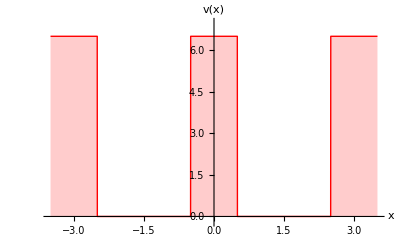

```mathematica
v[x]//Plot[#/.{v0->6.5(*Hartrees*),a->1, b->2(* in Bohr radius*)},{x,-3.5,3.5},
AxesLabel->{"x","v(x)"},
BaseStyle->{"FontFamily"->"Helvetica",FontSize->18},
PlotStyle->{Red,Thick},
PlotRange->{Automatic,{-0.2,7.0}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis
]&
```

```mathematica
Do[Subscript[c,i]=.,{i,8}];
Do[Subscript[ψ,i]=.,{i,5}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x]+Subscript[c, 3] Sin[β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x]+Subscript[c, 5] Exp[α x];
Subscript[ϕ, 4][x_]:=Subscript[c, 6] Cos[β x]+Subscript[c, 7] Sin[β x];
Subscript[ϕ, 5][x_]:=Subscript[c, 8] Exp[-α x];
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ψ_1 not found.

Unset::norep: Assignment on Subscript for ψ_2 not found.

Unset::norep: Assignment on Subscript for ψ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/.x->-a/2-b)==0;
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/.x->-a/2-b)==0;
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/.x->-a/2)==0;
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/.x->-a/2)==0;
eq[5]=(Subscript[ϕ, 3][x]-Subscript[ϕ, 4][x]/.x->a/2)==0;
eq[6]=(Subscript[ϕ, 3]'[x]-Subscript[ϕ, 4]'[x]/.x->a/2)==0;
eq[7]=(Subscript[ϕ, 4][x]-Subscript[ϕ, 5][x]/.x->a/2+b)==0;
eq[8]=(Subscript[ϕ, 4]'[x]-Subscript[ϕ, 5]'[x]/.x->a/2+b)==0;
```